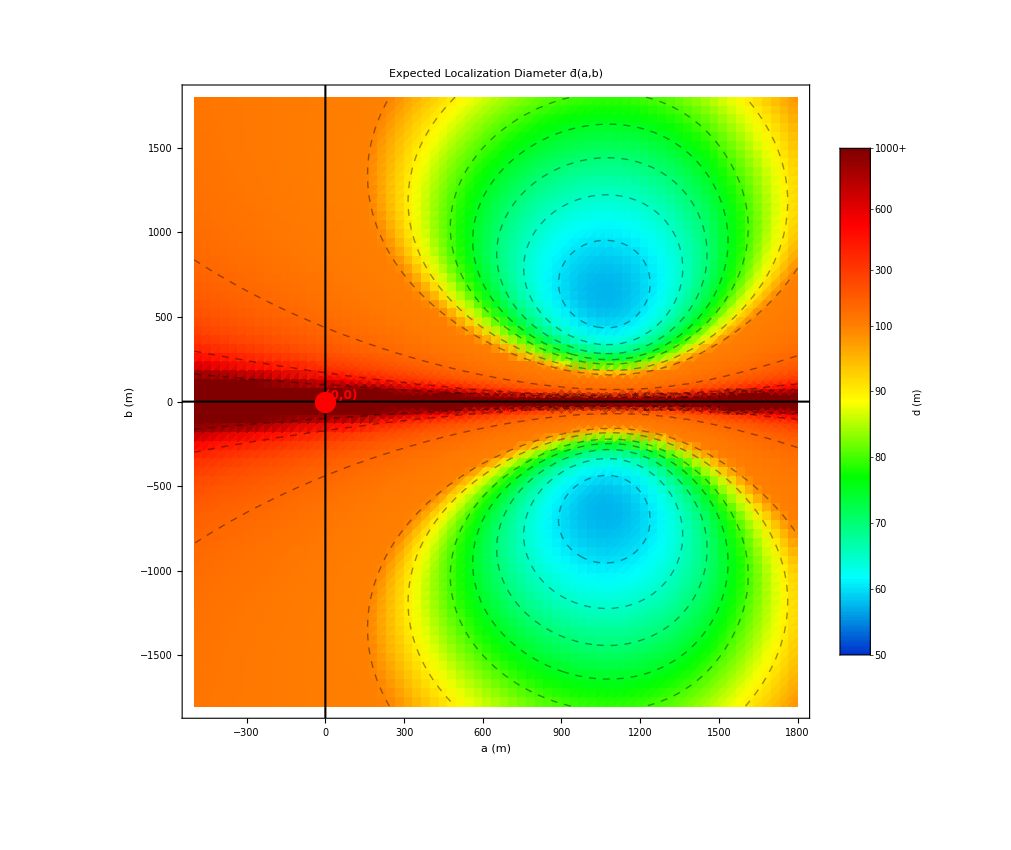

```mathematica
(* ============================================================*)(*Q2:期望定位区域直径 dbar(a,b) 的二维热力图*)(*带坐标轴、带图例，叠加等高线，导出为图片*)(* ============================================================*)(*----参数（与你原代码一致）----*)h=1500.;
alpha=1. Degree;

(*----两直线交点----*)
intersect2Lines[P1_,th1_,P2_,th2_]:=Module[{u1,u2,diff,denom,t1},u1={Cos[th1],Sin[th1]};
u2={Cos[th2],Sin[th2]};
diff=P2-P1;
denom=u1[[1]] u2[[2]]-u1[[2]] u2[[1]];
If[Abs[denom]<10^-8,Return[None]];
t1=(diff[[1]] u2[[2]]-diff[[2]] u2[[1]])/denom;
P1+t1 u1];

(*----交会四边形顶点----*)
quadVertices[x0_,a_,b_]:=Module[{P1={0.,0.},P2={a,b},dir,th2,thP,thM,v},dir={x0-a,-b};
If[Norm[dir]<10^-6,Return[None]];
th2=ArcTan[dir[[1]],dir[[2]]];
thP=th2+alpha;
thM=th2-alpha;
v={intersect2Lines[P1,alpha,P2,thP],intersect2Lines[P1,alpha,P2,thM],intersect2Lines[P1,-alpha,P2,thM],intersect2Lines[P1,-alpha,P2,thP]};
If[MemberQ[v,None],Return[None]];
v];

(*----四边形直径----*)
quadDiameter[verts_]:=Module[{n=Length[verts],mx=0.},Do[Do[mx=Max[mx,Norm[verts[[i]]-verts[[j]]]],{j,i+1,n}],{i,1,n}];
mx];

(*----期望直径----*)
expectedD[a_?NumericQ,b_?NumericQ,n_Integer:50]:=Module[{xs,fs,vals,total,totalW},xs=Table[h (k+0.5)/n,{k,0,n-1}];
fs=2. xs/h^2;
vals=Table[Module[{vs=quadVertices[xs[[k]],a,b]},If[vs===None,Indeterminate,quadDiameter[vs]]],{k,1,n}];
If[MemberQ[vals,Indeterminate],Return[Indeterminate]];
total=Total[fs vals];
totalW=Total[fs];
total/totalW];

(* ===1. 定义数值 d 到非线性参数 t∈[0,1] 的映射===*)ClearAll[tVal,colorFromT,customColorFunc,plot2D];

tVal[d_]:=Piecewise[{{0.,d<=50.},{0.65*((d-50.)/50.),50.<d<=100.},{0.65+0.35*((d-100.)/900.),100.<d<=1000.},{1.0,d>1000.}}];

(* ===2. 核心修复：采用 {数值,颜色} 双元素列表，决不使用->符号===*)
colorFromT[t_]:=Blend[{{0.00,RGBColor[0,0.2,0.8]},{0.15,Cyan},{0.35,Green},{0.50,Yellow},{0.65,Orange},{0.85,Red},{1.00,RGBColor[0.5,0,0]}},t];

customColorFunc[d_]:=colorFromT[tVal[d]];

(* ===3. 绘图主体===*)
plot2D=Show[(*底层：热力图*)DensityPlot[expectedD[a,b,50],{a,-500,1800},{b,-1800,1800},PlotRange->All,PlotPoints->70,MaxRecursion->1,ColorFunctionScaling->False,ColorFunction->customColorFunc,Frame->True,FrameLabel->{Style["a (m)",16,Bold,Black],Style["b (m)",16,Bold,Black]},FrameStyle->Directive[Black,12],FrameTicksStyle->Directive[Black,12],PlotLabel->Style["Expected Localization Diameter \!\(\*OverscriptBox[\(d\), \(_\)]\)(a,b)",18,Bold,Black],(*图例*)PlotLegends->BarLegend[{colorFromT,{0,1}},Ticks->{{0.00,"50"},{0.13,"60"},{0.26,"70"},{0.39,"80"},{0.52,"90"},{0.65,"100"},{0.76,"300"},{0.88,"600"},{1.00,"1000+"}},LegendLabel->Style["d (m)",12,Bold]],Mesh->None,BoundaryStyle->None],(*中层：等高线*)ContourPlot[expectedD[a,b,50],{a,-500,1800},{b,-1800,1800},PlotRange->All,PlotPoints->70,MaxRecursion->1,Contours->{50,55,60,65,70,75,80,90,100,200,500,1000},ContourShading->None,ContourStyle->Directive[Black,Opacity[0.4],Dashed]],(*上层：坐标轴与原点 (0,0) 标记*)Graphics[{Directive[Black,AbsoluteThickness[1.5]],InfiniteLine[{{0,0},{1,0}}],InfiniteLine[{{0,0},{0,1}}],Directive[Red,AbsoluteThickness[2]],PointSize[0.018],Point[{0,0}],Text[Style[" (0,0) ",12,Bold,Red,Background->White],{0,0},{-1.2,-1.2}]}],ImageSize->850];

(*显示图形*)
plot2D

(* ===4. 导出 PNG===*)
exportPathPNG=FileNameJoin[{NotebookDirectory[],"Q2_expected_diameter_heatmap.png"}];
Export[exportPathPNG,plot2D,ImageResolution->300];
```

```mathematica
Directory[]                          (*查看当前工作目录*)
AbsoluteFileName["Q2_expected_diameter_heatmap.png"]  (*查看该文件的绝对路径*)
```

C:\Users\lenovo

C:\Users\lenovo\Q2_expected_diameter_heatmap.png